## Background

```mathematica
rawMetadata=Import["/Users/katjad/Documents/Github/SheepCapstone/Salt6_corners_food locations_collective decision making_March2019.csv"];
```

```mathematica
paddock=rawMetadata[[-4;;-1,-2;;-1]];
feeding=rawMetadata[[2;;11,-2;;-1]];
water=rawMetadata[[12,-2;;-1]];
```

```mathematica
paddockRegion=BoundaryDiscretizeGraphics[Polygon[paddock]];metadataGraphic=Graphics[{LightBrown,Polygon[paddock],Darker[Green],Circle[#,30]&/@feeding,Thick,Darker[Blue],Circle[water,50]}];
```

```mathematica
rawXs=Import["/Users/katjad/Documents/Github/SheepCapstone/xs.csv"];
rawYs=Import["/Users/katjad/Documents/Github/SheepCapstone/ys.csv"];
rawIDs=Import["/Users/katjad/Documents/Github/SheepCapstone/ids.csv"];
rawTs=Import["/Users/katjad/Documents/Github/SheepCapstone/ts.csv"];
rawTsStart=Import["/Users/katjad/Documents/Github/SheepCapstone/period.start.idxs.csv"];
```

```mathematica
Dimensions[rawXs]
```

{52,210352}

```mathematica
rawCoordinates=Table[{rawXs[[x,y]],rawYs[[x,y]]},{x,2,52},{y,2,210352}]/."NA"->Missing[];
```

## Closeness within radius

```mathematica
rawCoordinates2=rawCoordinates/.Missing[]->Indeterminate
```

{{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},210343,{582412.,6.56368×10^6},{582415.,6.56368×10^6},{582418.,6.56368×10^6},{Indeterminate,Indeterminate}},49,{1}}
 |  |  |  |

```mathematica
rawCoordinates2[[3]]
```

{{Indeterminate,Indeterminate},{580434.,6.56368×10^6},{580439.,6.56368×10^6},{580444.,6.56367×10^6},210343,{582368.,6.56357×10^6},{582368.,6.56357×10^6},{582369.,6.56356×10^6},{Indeterminate,Indeterminate}}
 |  |  |  |

```mathematica
distances[a_,b_]:=Sqrt[Total[(rawCoordinates2[[a]] - rawCoordinates2[[b]])^2,{2}]]
```

```mathematica
nf=Nearest[DeleteMissing[MapIndexed[#1->#2[[1]]&,rawCoordinates[[All,5000]]],1,3]]
```

NearestFunction[…]

```mathematica
nf[rawCoordinates[[4,5000]],{All,200}]
```

{4,42,26,34,44,39,41,25,19,8,13,23}

```mathematica
SingleSheepWithinRadius[100,4,4000]
```

{4,44,23,19,26,25,8,39,13,41,34,42,16,5,45,17,2,11}

```mathematica
SingleSheepWithinRadius[radius_,sheep_,time_]:=
If[rawCoordinates[[sheep,time]]==={Missing[],Missing[]},
Missing[],Nearest[DeleteMissing[MapIndexed[#1->#2[[1]]&,rawCoordinates[[All,time]]],1,3],rawCoordinates[[sheep,time]],{All,radius}]]
```

```mathematica
RepeatedTiming[SingleSheepWithinRadius[100,4,4000],3]
```

{0.0003,{4,44,23,19,26,25,8,39,13,41,34,42,16,5,45,17,2,11}}

```mathematica
sheep1herdsize=With[{herd=SingleSheepWithinRadius[100,1,#]},If[MissingQ[herd],Missing[],Length[herd]]]&/@Range[Length[rawCoordinates[[4]]]];
```

24.4138

22

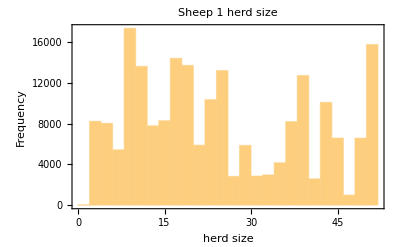

-Graphics-

```mathematica
Mean[DeleteMissing[sheep1herdsize]]//N
Median[DeleteMissing[sheep1herdsize]]
Histogram[sheep1herdsize,PlotLabel->"Sheep 1 herd size",Frame->True,FrameLabel->{"herd size","Frequency"}]
ListLinePlot[sheep1herdsize,PlotLabel->"Sheep 1 herd size over time",Frame->True,FrameLabel->{"time","herd size"}]
```

```mathematica
sheep2herdsize=With[{herd=SingleSheepWithinRadius[100,2,#]},If[MissingQ[herd],Missing[],Length[herd]]]&/@Range[Length[rawCoordinates[[4]]]];
```

20.7669

15

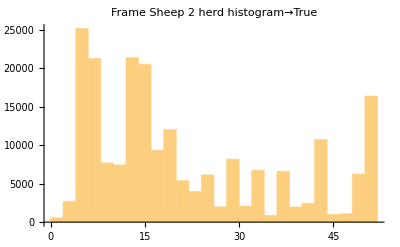

-Graphics-

```mathematica
Mean[DeleteMissing[sheep2herdsize]]//N
Median[DeleteMissing[sheep2herdsize]]
Histogram[sheep2herdsize,PlotLabel->"Sheep 2 herd histogram",Frame->True,FrameLabel->{"herd size","Frequency"}]
ListLinePlot[sheep2herdsize,PlotLabel->"Sheep 2 herd size over time",Frame->True,FrameLabel->{"time","herd size"}]
```

```mathematica
allSheepHerdSize100=Table[With[{herd=SingleSheepWithinRadius[100,x,#]},If[MissingQ[herd],Missing[],Length[herd]]]&/@Range[Length[rawCoordinates[[x]]]],{x,1,51}];
```

```mathematica
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/allSheepHerdSize100.mx",allSheepHerdSize100]
```

/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/allSheepHerdSize100.mx

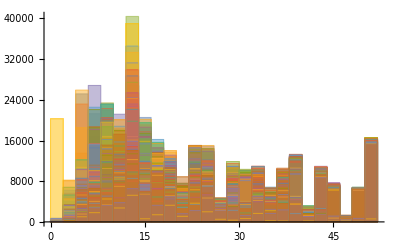

```mathematica
Histogram[allSheepHerdSize100]
```

```mathematica
stats=Prepend[Transpose[Prepend[{N[Mean[DeleteMissing[#]],3],Median[DeleteMissing[#]]}&/@allSheepHerdSize100,{"Mean","Median"}]],Prepend[Range[51],"sheep"]];
```

```mathematica
stats
```

{{{sheep},1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51},{Mean,24.4,20.8,24.4,26.4,25.7,23.9,23.7,25.1,24.3,23.8,23.,25.,23.9,26.3,25.2,23.4,25.9,25.3,26.9,23.3,25.7,23.1,11.,23.7,23.8,23.9,24.5,25.2,25.,24.1,25.4,25.2,24.8,25.7,24.8,24.8,23.,23.3,24.2,24.1,25.9,25.4,24.1,25.2,25.1,22.1,24.5,26.8,25.5,29.,25.8},{Median,22,15,21,25,25,20,21,23,22,18,18,22,21,25,22,18,24,24,25,20,23,18,8,19,21,23,22,22,21,20,23,23,22,25,22,23,18,18,22,22,25,23,20,23,23,18,22,25,24,28,23}}

```mathematica
Grid[stats[[All,1;;21]],Frame->All]
```

sheep | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
Mean | 24.4 | 20.8 | 24.4 | 26.4 | 25.7 | 23.9 | 23.7 | 25.1 | 24.3 | 23.8 | 23. | 25. | 23.9 | 26.3 | 25.2 | 23.4 | 25.9 | 25.3 | 26.9 | 23.3
Median | 22 | 15 | 21 | 25 | 25 | 20 | 21 | 23 | 22 | 18 | 18 | 22 | 21 | 25 | 22 | 18 | 24 | 24 | 25 | 20

## DBScan

```mathematica
Animate[Show[metadataGraphic,Graphics[Circle[#,15]&/@DeleteMissing[rawCoordinates[[All,n]],1,2],PlotRange->RegionBounds[paddockRegion]]],{n,1,200000,25}]
```

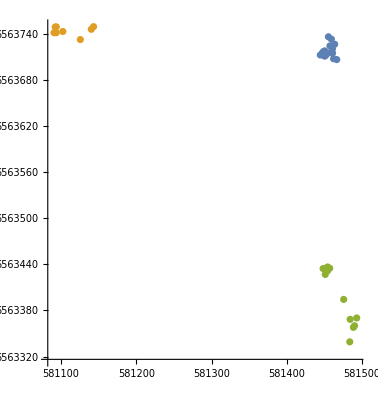

```mathematica
ListPlot[FindClusters[DeleteMissing[rawCoordinates[[All,1000]],1,2],Method->{"DBSCAN","NeighborhoodRadius"->50},DistanceFunction->EuclideanDistance],AspectRatio->Automatic]
```

```mathematica
dbScanClusters[time_,radius_]:=
Module[{positions,rawClusters,outliers},
positions=DeleteMissing[MapIndexed[#1->#2[[1]]&,rawCoordinates[[All,time]]],1,3];
rawClusters=FindClusters[positions,Method->{"DBSCAN","NeighborhoodRadius"->radius,"DropAnomalousValues"->True},DistanceFunction->EuclideanDistance];
outliers=Complement[Values[positions],Flatten[rawClusters]];
Append[rawClusters,outliers]]
```

```mathematica
dbScanClusters[1000,200]
```

{{2,4,5,6,8,10,11,17,22,23,26,28,29,31,32,35,40,41,44,45,46,49},{3,7,9,20,21,36,38,48},{12,14,16,18,24,25,33,34,37,39,42,47,51},{}}

```mathematica
dbScanHerds50=Table[dbScanClusters[x,50],{x,1,Length[rawCoordinates[[1]]]}];
```

```mathematica
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds50.mx",dbScanHerds50]
```

```mathematica
dbScanHerds100=Table[dbScanClusters[x,100],{x,1,Length[rawCoordinates[[1]]]}]
```

{{{5,8,17,21,22,33,35,38,40,44,48},{}},{{2,3,4,5,7,8,9,10,11,12,14,16,17,18,19,20,21,22,23,24,25,26,27,29,31,33,34,35,36,37,38,39,40,41,42,44,45,46,47,48,51},{}},210348,{{2,12,16,39,44,50},{5,40,51},{7,8,31,46},{21},{}}}
 |  |  |  |

```mathematica
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds100.mx",dbScanHerds100]
```

/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds100.mx

```mathematica
dbScanHerds75=Table[dbScanClusters[x,75],{x,1,Length[rawCoordinates[[1]]]}]
```

```mathematica
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds75.mx",dbScanHerds75]
```

/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds75.mx

```mathematica
dbScanHerds5=Table[dbScanClusters[x,5],{x,1,Length[rawCoordinates[[1]]]}];
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds5.mx",dbScanHerds5]
```

/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds5.mx

```mathematica
dbScanHerds10=Table[dbScanClusters[x,10],{x,1,Length[rawCoordinates[[1]]]}];
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds10.mx",dbScanHerds10]
```

$Aborted

/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds10.mx

```mathematica
dbScanHerds20=Table[dbScanClusters[x,10],{x,1,Length[rawCoordinates[[1]]]}];
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds20.mx",dbScanHerds20]
```

/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds20.mx

```mathematica
dbScanHerds5=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds5.mx"];
dbScanHerds10=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds10.mx"];
dbScanHerds50=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds50.mx"];
dbScanHerds100=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds100.mx"];
```

```mathematica
Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds10.mx"]
```

dbScanHerds10

Persistent homology

```mathematica
allHerdSizes5=Length/@Catenate[dbScanHerds5[[All,1;;-2]]];
allHerdSizes10=Length/@Catenate[dbScanHerds10[[All,1;;-2]]];
allHerdSizes20=Length/@Catenate[dbScanHerds20[[All,1;;-2]]];
allHerdSizes50=Length/@Catenate[dbScanHerds50[[All,1;;-2]]];
allHerdSizes100=Length/@Catenate[dbScanHerds100[[All,1;;-2]]];
```

```mathematica
allHerdSizes10
```

Catenate[0]

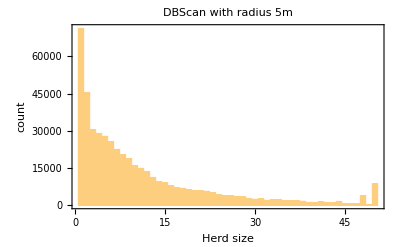

```mathematica
Histogram[allHerdSizes5,{1},Frame->True, FrameLabel->{"Herd size","count"},PlotLabel->"DBScan with radius 5m"]
```

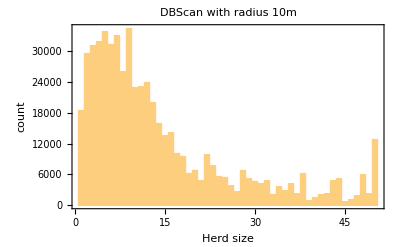

```mathematica
Histogram[allHerdSizes10,{1},Frame->True, FrameLabel->{"Herd size","count"},PlotLabel->"DBScan with radius 10m"]
```

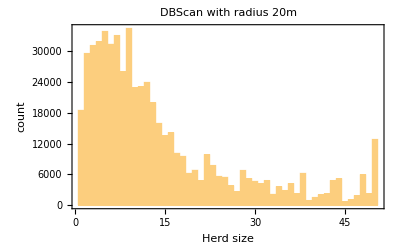

```mathematica
Histogram[allHerdSizes20,{1},Frame->True, FrameLabel->{"Herd size","count"},PlotLabel->"DBScan with radius 20m"]
```

```mathematica
Histogram[allHerdSizes10,{1},Frame->True, FrameLabel->{"Herd size","count"},PlotLabel->"DBScan with radius 10m"]
```

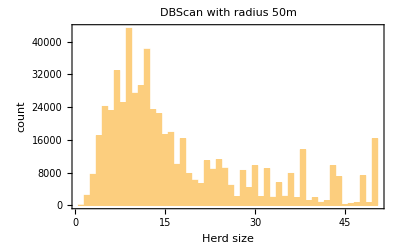

```mathematica
Histogram[allHerdSizes50,{1},Frame->True, FrameLabel->{"Herd size","count"},PlotLabel->"DBScan with radius 50m"]
```

```mathematica
allHerdSizes75=Length/@Catenate[dbScanHerds75[[All,1;;-2]]];
```

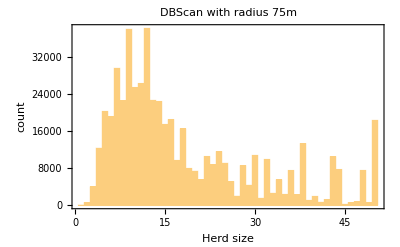

```mathematica
Histogram[allHerdSizes75,{1},Frame->True, FrameLabel->{"Herd size","count"},PlotLabel->"DBScan with radius 75m"]
```

```mathematica
allHerdSizes100=Length/@Catenate[dbScanHerds100[[All,1;;-2]]];
```

```mathematica
Histogram[allHerdSizes100,{1},Frame->True, FrameLabel->{"Herd size","count"},PlotLabel->"DBScan with radius 100m"]
```

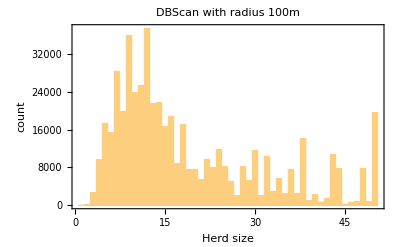

```mathematica
herdSizeDbScan[sheep_,cluster_]:=
Which[FreeQ[Catenate[cluster],sheep],Missing[],
	MemberQ[cluster[[-1]],sheep],0,
	True,Length[SelectFirst[cluster,MemberQ[sheep]]]]
```

```mathematica
dbScanSheep1=herdSizeDbScan[1,#]&/@dbScanHerds50;
```

24.3689

22

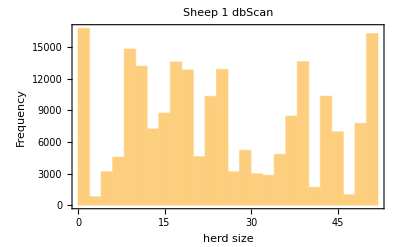

-Graphics-

```mathematica
Mean[DeleteMissing[dbScanSheep1]]//N
Median[DeleteMissing[dbScanSheep1]]
Histogram[dbScanSheep1,PlotLabel->"Sheep 1 dbScan",Frame->True,FrameLabel->{"herd size","Frequency"}]
ListLinePlot[dbScanSheep1,PlotLabel->"Sheep 1 dbScan over time",Frame->True,FrameLabel->{"time","herd size"}]
```

```mathematica
dbScan20sheep=Table[herdSizeDbScan[x,#]&/@dbScanHerds50,{x,1,20}];
```

```mathematica
dbScanStats=Prepend[Transpose[Prepend[{N[Mean[DeleteMissing[#]],3],Median[DeleteMissing[#]]}&/@dbScan20sheep,{"Mean","Median"}]],Prepend[Range[20],"sheep"]];
```

```mathematica
Grid[dbScanStats,Frame->All]
```

sheep | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
Mean | 24.4 | 20. | 24. | 26.7 | 26. | 24. | 23.5 | 25.1 | 24.3 | 23.7 | 23.1 | 24.5 | 23.8 | 26.3 | 25.1 | 22.9 | 25.9 | 25.1 | 26.9 | 22.9
Median | 22 | 16 | 22 | 25 | 25 | 22 | 22 | 23 | 22 | 18 | 20 | 22 | 22 | 25 | 24 | 19 | 24 | 24 | 25 | 20

## Dimension Reduction

### Linear

```mathematica
sample=Downsample[rawCoordinates2,{1,100,1}];
```

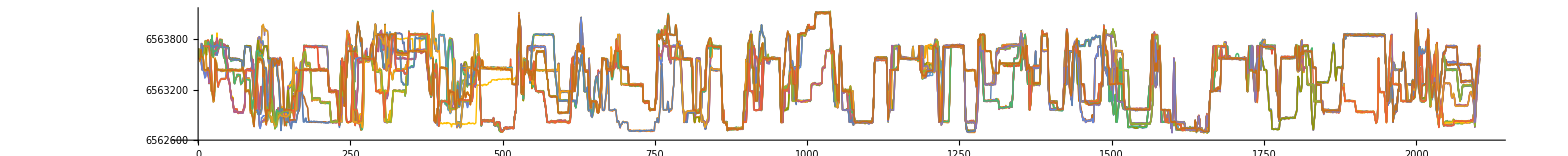

```mathematica
ListLinePlot[sample[[All,All,2]],PlotStyle->Thin,AspectRatio->1/10,ImageSize->2000]
```

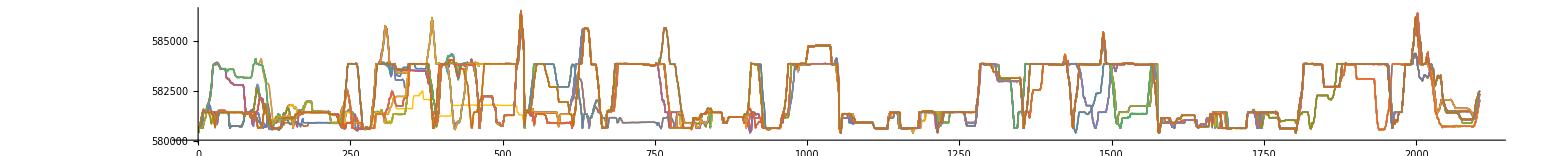

```mathematica
ListLinePlot[sample[[All,All,1]],PlotStyle->Thin,AspectRatio->1/10,ImageSize->2000]
```

```mathematica
trainingData=RandomSample[DeleteMissing[Catenate[rawCoordinates],1,2],10000];
```

```mathematica
dr=DimensionReduction[trainingData,1]
```

DimensionReducerFunction[…]

```mathematica
dr[rawCoordinates[[2,1;;10]]]
```

{{0.},{0.271379},{0.272962},{0.27288},{0.272763},{0.272986},{0.274089},{0.276985},{0.279798},{0.282504}}

```mathematica
drSample=(dr/@sample)[[All,All,1]];
```

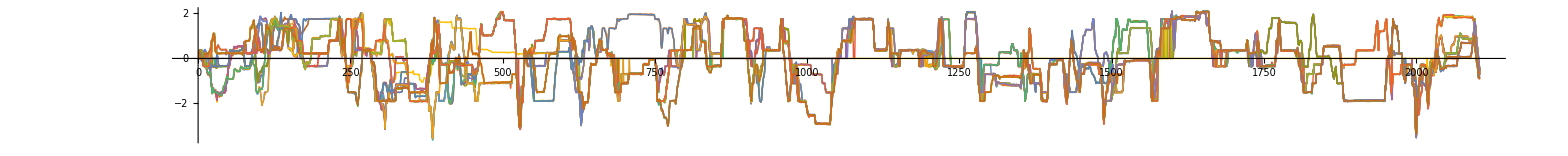

```mathematica
ListLinePlot[drSample,PlotStyle->Thin,AspectRatio->1/10,ImageSize->2000]
```

### TSNE

```mathematica
tsne=DimensionReduction[trainingData,1,Method-> "TSNE"]
```

$Aborted

```mathematica
tsne[rawCoordinates[[2,1;;10]]]
```

```mathematica
tsneSample=(dr/@sample)[[All,All,1]];
```

```mathematica
ListLinePlot[drSample,PlotStyle->Thin,AspectRatio->1/10,ImageSize->2000]
```